```mathematica
Integrate[Exp[-r^2/(2 w^2)]2 Pi r (2/Sqrt[r^2+z^2]-1/Sqrt[r^2+(z+d)^2]-1/Sqrt[r^2+(z-d)^2]),{r,0,Infinity}]/d^2
```

ConditionalExpression[1/(d^2 √(1/w^2))√2 π^(3/2) (-ⅇ^((d-z)^2/(2 w^2)) √(1/(d-z)^2) √((d-z)^2)+2 ⅇ^(z^2/(2 w^2)) √(1/z^2) √(z^2)-ⅇ^((d+z)^2/(2 w^2)) √(1/(d+z)^2) √((d+z)^2)+ⅇ^((d-z)^2/(2 w^2)) √(1/(d-z)^2) √((d-z)^2) Erf[(√(1/w^2))/(√2 √(1/(d-z)^2))]-2 ⅇ^(z^2/(2 w^2)) √(1/z^2) √(z^2) Erf[(√(1/w^2))/(√2 √(1/z^2))]+ⅇ^((d+z)^2/(2 w^2)) √(1/(d+z)^2) √((d+z)^2) Erf[(√(1/w^2))/(√2 √(1/(d+z)^2))]), ]

```mathematica
FullSimplify[Out[1]/.{z->zd * d, d->dn*w },Assumptions->{z>0, d>0,w>0,dn>0,zd>0}]
```

ConditionalExpression[(√2 ⅇ^((d zd (-2 dn w+d zd))/(2 w^2)) π^(3/2) (2 ⅇ^((d dn zd)/w) Erfc[(d zd)/(√2 w)]-ⅇ^(dn^2/2) (ⅇ^((2 d dn zd)/w) Erfc[(dn w+d zd)/(√2 w)]+Erfc[Abs[dn w-d zd]/(√2 w)])))/(dn^2 w), dn w≠d zd]

```mathematica
Limit[(√2 ⅇ^(zw^2/2) π^(3/2) (2 Erfc[zw/(√2)]-ⅇ^(dn^2/2) (ⅇ^(dn zw) Erfc[(dn +zw)/(√2)]+ⅇ^(-dn zw) Erfc[Abs[dn -zw]/(√2)])))/(dn^2 w),dn->0,Assumptions->{w>0,zw>0}]
```

(π (2 zw-ⅇ^(zw^2/2) √(2 π) (1+zw^2) Erfc[zw/(√2)]))/w

```mathematica
Limit[(Out[1]-Out[2])/d,dn->0]
```

ConditionalExpression[Undefined, ]

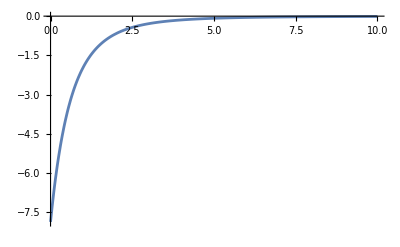

```mathematica
Plot[π (2 zw-ⅇ^(zw^2/2) √(2 π) (1+zw^2) Erfc[zw/(√2)]),{zw,0,10},PlotRange->All]
```

```mathematica
(π (2 zw-ⅇ^(zw^2/2) √(2 π) (1+zw^2) Erfc[zw/(√2)]))/w/.zw->0
```

-(√2 π^(3/2))/w